# Example 5.14 p138

We rewrote the function x^(α-1)/(1+x) to get the branch cut lined up on the real axis.

```mathematica
Clear[α]
Integrate[x^(α-1)/(1+x) ,{x,0, ∞}]
```

ConditionalExpression[π Csc[π α], 0<Re[α]<1]

```mathematica
f[α_][z_]:=ⅇ^((α-1)(Log[-z]-ⅈ π))/(1+z)
TabView[
{"6"->ComplexPlot3D[f[6][z],{z, 2}],
"2"->ComplexPlot3D[f[2][z],{z, 2},PlotRange->{0,23}],
"1/3"->ComplexPlot3D[f[1/3][z],{z, 2},
PlotRange->{0,23}],
"-1"->ComplexPlot3D[f[-1][z],{z, 2},
PlotRange->{0,23}],
"-1.562"->ComplexPlot3D[f[-1.562][z],{z, 2},
PlotRange->{0,23}],
"-1.5"->ComplexPlot3D[f[-1.5][z],{z, 2},
PlotRange->{0,23}],
"-3/2"->ComplexPlot3D[f[-3/2][z],{z, 2},
PlotRange->{0,23},
PlotLegends->Automatic]
}]
```

1234567

We are going to do the key hole contour below. We need to make sure we can:
A) Evaluate the ∫_Γ f(z)dz using residues.
B) Understand what happens on the inner circle as ϵ→0^+
C) Understand what happens on the outer circle as R→∞
D) Understand what happens across the branch cut along the real axis.

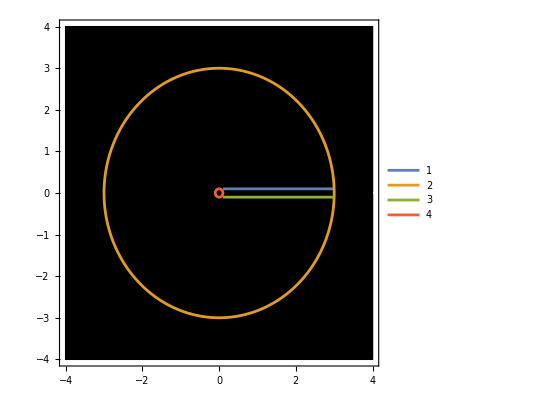

```mathematica
p1[t_]:=ϵ(1+ⅈ) + (R-ϵ)t 
p2[t_]:=R E^(2π ⅈ t)
p3[t_]:= R-ϵ ⅈ-(R-ϵ) t
p4[t_]:=ϵ E^(-2π ⅈ t)
α=-1.5;
{R,ϵ}={3,0.1};
Show[
ComplexPlot[f[α][z],{z,4}],
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]],ReIm[p3[t]],ReIm[p4[t]]},{t,0,1},
PlotLegends->Automatic],
Epilog->Point[{-1,0}]
]
```

We need to understand the jump across the branch cut. The branch cut is needed because of the Log.  Logs jump by 2π ⅈ when you go cross a branch cut.  We have
	ⅇ^((α-1)(Log[-x]+ 2 π ⅈ ))/(1+x)=(ⅇ^((α-1)Log[-x])ⅇ^(2(α-1)π ⅈ))/(1+x)=ⅇ^(2(α-1)π ⅈ)ⅇ^((α-1)Log[-x])/(1+x)=ⅇ^(2(α-1)π ⅈ)f[x]
Lets check

```mathematica
f[α_][z_]:=ⅇ^((α-1)(Log[-z]-ⅈ π))/(1+z)
{α,δ}={2.2,0.0000001};
ⅇ^((α-1)2π ⅈ)
TableForm[Table[(f[α][x-δ ⅈ])/(f[α][x+δ ⅈ]),{x,1,5,0.2}]]
```

0.309017+0.951057 ⅈ

0.309017+0.951056 ⅈ
0.309017+0.951056 ⅈ
0.309017+0.951056 ⅈ
0.309017+0.951056 ⅈ
0.309017+0.951056 ⅈ
0.309017+0.951056 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ
0.309017+0.951057 ⅈ

OK we understand the branch cut jump.  The first bit converges to the thing we want
	∫_Γ_1 f dz=∫_ϵ^R f(z)dz→∫_0^∞ f(x+0^+I)dz:=Int_1
and the third bit 
	∫_Γ_3 f dz=∫_R^ϵ f(z)dz→-∫_0^∞ f(x-0^+I)dz
and 
	-∫_0^∞ f(x-0^+I)dz=-ⅇ^(-(α-1)2π ⅈ)∫_0^∞ f(x+0^+I)dz=-ⅇ^(-(α-1)2π ⅈ) Int_1

As x→∞
	x^(α-1)/(1+x)~x^(α-1)/x=x^(α-2)
so the integral round the big circle
	∫_Γ_2 f dz=∫_0^1 f(R ⅇ^(2π ⅈ t))R 2π ⅈ ⅇ^(2π ⅈ t)dt=Int_2
satisfies
	|Int_2|≤2π R R^(α-2)=2π R^(α-1)->0 
provided α-1<0.

As x→0
	x^(α-1)/(1+x)~x^(α-1)/1=x^(α-1)
so the integral round the little circle
	∫_Γ_4 f dz=∫_0^1 f(ϵ ⅇ^(-2π ⅈ t))(-ϵ 2π ⅈ )ⅇ^(-2π ⅈ t)dt=Int_4
satisfies
	|Int_4|≤2π ϵ ϵ^(α-1)=2π ϵ^α->0 
provided α>0.

Now the easy bit.  There is a single enclosed pole of
	ⅇ^((α-1)(Log[-z]-ⅈ π))/(1+z)
at z_1=-1. The residue is simply the thing on top evaluated at z=-1 so 
	r_1=Res(f,-1)=ⅇ^((α-1)(Log[1]-ⅈ π))=ⅇ^(ⅈ π (1-α)).  
So ∫_(Γ_1+Γ_2+Γ_3+Γ_4) f(z)dz=2π ⅈ ⅇ^(ⅈ π (1-α))  if 0<ϵ<1 and R>1.

Assembling all the bits as ϵ->0 and R→∞
	∫_Γ_1 f(z)dz+∫_Γ_2 f(z)dz+∫_Γ_3 f(z)dz+∫_Γ_4 f(z)dz=2π ⅈ ⅇ^(ⅈ π (1-α))
If 0<α<1 then as ϵ->0 and R→∞ the integrals on the circles (Γ_2 and Γ_4) go to zero
	∫_Γ_1 f(z)dz+∫_Γ_3 f(z)dz=2π ⅈ ⅇ^(ⅈ π (1-α))
We gave names to these bits and worked out the connection
	 Int_1+Int_3=Int_1(1-ⅇ^(-(α-1)2π ⅈ))=2π ⅈ ⅇ^(ⅈ π (1-α)).
If α<0 then the integral below converges and 
	Int_1=∫_0^∞ x^(α-1)/(1+x)dx=(2π ⅈ ⅇ^(ⅈ π (1-α)))/(1 - ⅇ^(-(α-1)2π ⅈ))

```mathematica
Clear[α]
F1[α_]=Integrate[x^(α-1)/(1+x),{x,0, ∞}]
F2[α_]:=(2π ⅈ ⅇ^(ⅈ π (1-α)))/(1-ⅇ^(-(α-1)2π ⅈ))
```

ConditionalExpression[π Csc[π α], 0<Re[α]<1]

Here is where we should check carefully!  There are a lot of details etc.

```mathematica
α=0.3

;
F1[α]
F2[α]
```

3.88322

-3.88322+0. ⅈ